```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
U[x_,y_]=100000/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
(*DECAYENERGY=.2;
DECAYDT=.2;*)
CHAINS=10;
STEPS=10;
```

10019707.097.707650.3648780.4047385.4099712.52.24408×10^80.00004052650.000139908True{1,2,4,9}{1,3,11}

20021.91163×10^6-0.03168510.2527480.3810497.504223749.151.91164×10^60.00004903710.00125278False{1,4,9,11}{1,11}

30032323.168.656910.3386380.3680758.533952331.734913.80.00007179520.0084281True{1}{2,11}

40043900.3826.14040.8909540.3136934.01705821.8463904.40.0001399080.016424False{1,2,3,11}{1,11}

5005345.6378.246660.4534280.4734967.0399352.6771509.50.0001692890.0240463True{1,4,11}{1,2,3,5,11}

60061500.530.2483910.5651370.3517958.96409352.6771509.50.0001692890.0240463False{1,4,11}{1,2,3,5,11}

7007341.39913.07410.2499160.34280311.278352.6771509.50.0001692890.0240463True{1,4,11}{1,2,3,5,11}

80081506.32-3.543390.8924920.3139143.17742352.6771509.50.0001692890.0240463False{1,4,11}{1,2,3,5,11}

9009344.7319.544560.380860.4286047.94661352.6771509.50.0001692890.0240463True{1,4,11}{1,2,3,5,11}

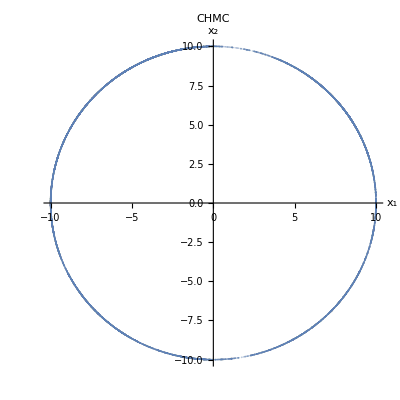

```mathematica
INTERVAL=1001;
(*DECAYENERGY=0.0001*)

QS=hmc[U,dU,ddU,2,5000,10000,True,True,{}];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->CHMC]
```

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False,{}];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->HMC]
```

10012732.2811.43360.4039590.4589115.326372737.617.65681×10^70.00005394081.×10^-7True{1,2,3,4,11}{1,11}

20021273.258.109980.2578630.3362156.22681279.477.65681×10^70.00009555941.×10^-7True{1,2,3,5,6}{1,11}

3003408.2169.131930.3337290.4212432.97043411.1877.65681×10^70.0001399081.×10^-7True{1,3,5,6,11}{1,11}

```mathematica
Covariance[QS]
```

{{71.9735,-11.5157},{-11.5157,22.7858}}

```mathematica
Exp[-1/9 1/2(√(x^2+y^2)-10)^2]//TraditionalForm
```

ⅇ^(-1/18 (√(x^2+y^2)-10)^2)

```mathematica
ⅇ^(-1/2((√(x^2+y^2)-10)^2)/10)
```

ⅇ^(-1/20 (-10+√(x^2+y^2))^2)

```mathematica
U[x_,y_]=0.1 1/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QS=hmc[U,dU,ddU,2,5000,10000,False,False,{}];
```

100124.9426170.6530.7041030.4707984.0069822.672428.94961.×10^-70.1752False{1,4}{1,4}

200211.282888.91290.07940910.01640791.9005722.672413.18331.×10^-70.307508False{1,4}{1,4}

30037.9377967.49590.6429210.3536763.9133722.672411.85121.×10^-70.313506False{1,4}{2,4}

400410.024999.26270.4597760.5048261.7732322.672411.79811.×10^-70.313939False{1}{2,3,4}

500511.7869-43171.10.6614850.5729160.0087386422.672411.79561.×10^-70.314001False{1}{2,3,4}

$Aborted

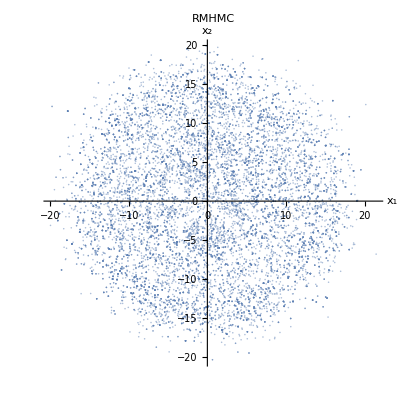

```mathematica
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.5],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->RMHMC]
```